# Array Differentiate

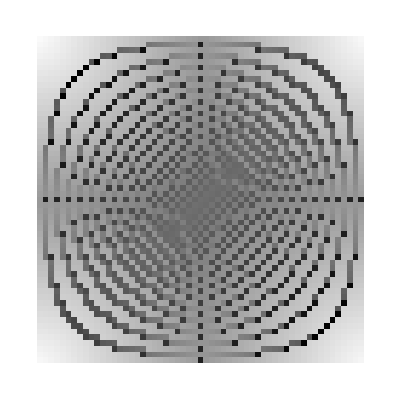

```mathematica
ArrayDiff[A_]:=Table[
Sqrt[(A[[i,j]]-A[[i+1,j]])^2+(A[[i,j]]-A[[i,j+1]])^2],
{i,1,Length[A[[1]]]-1},{j,1,Length[A[[1]]]-1}]
ArrayPlot[ArrayDiff[data]]
```

```mathematica
n=100;
data=Table[Mod[i*j,Prime[n]],{i,1,Prime[n]-1},{j,1,Prime[n]-1}];
ArrayPlot[
ArrayDiff[Table[Mod[i*j,Prime[n]],{i,1,Prime[n]-1},{j,1,Prime[n]-1}]],
AspectRatio->1,ImageSize->Large]
```

-Graphics-